# Processing of data generated by program HighWay

The notebook should be saved in the directory containing the files with data from the simulation

```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/scholtz/Dropbox/students/vanis/highway_x

It is expected that the files with data have extension “.hw”. This is the list of such files in current directory:

```mathematica
FileNames["*.hw"]
```

{}

Choose the file you want to load

```mathematica
fileName = "sim1.hw";
dataBrut = Import[fileName, "Table"];
data  = Transpose[ Delete[Transpose[dataBrut], 1]];
tMax = Length[data]
```

1102

We need to know how long the highway is, this is stored in hwLength and must be entered by hand. In what follows we divide the highway of length hwLength into the segments with length L. Then we calculate how many cars are inside the segment anc comput the distribution function.

```mathematica
hwLength = 5000;  (* the length of the highway in meters *)
L = 100; (* the length of the segment *)
```

```mathematica
FindDistribution[data_/;ListQ[data], hwLength_, L_]  := Module[{segments,number,ys,mids},
(segments= Table[ n , {n, 0, hwLength, L}]);
number= Length[data];
ys=Table[ Length[
Select[ data, segments[[n]] ≤ #<segments[[n+1]]&]]
/number, {n, 1, Length[segments]-1}];
mids = Table[ (segments[[n]]+segments[[n+1]])/2, {n, 1, Length[segments]-1}];
Transpose[ {mids, ys}]
]
distribution[n_] := FindDistribution[data[[n]], hwLength, L]
DrawDistribution[t_] :=Module[{},ListLinePlot[distribution[t], AxesOrigin->{0,0},
PlotRange -> {{0, 1000}, {0, 1}}]]
```

```mathematica
Animate[DrawDistribution[n], {n, 1, Length[data],1}]
```

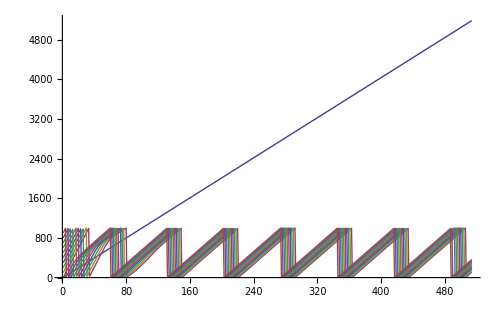

```mathematica
ListLinePlot[Transpose[dataBrut], PlotRange->Full]
```

```mathematica
Manipulate[Histogram[data[[n]], {0, 1000, 100}, AxesOrigin->{0,0}, PlotRange->{{0, 1000}, {0, 20}}], {n, 1, Length[data], 1}]
```

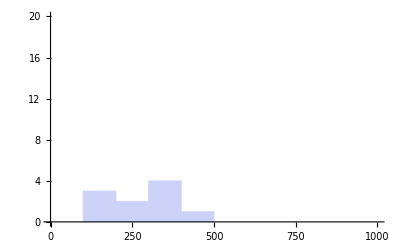

```mathematica
Histogram[data[[90]], {0, 1000, 100}, AxesOrigin->{0,0}, PlotRange->{{0, 1000}, {0, 20}}]
```